```mathematica
(*This notebook is used to generate figure 5 in the article
"The failure of propagation in heterogeneous reaction-diffusion systems through the method of upper and lower solutions" by 
Courdurier M. and Paduro E.*)
SetDirectory[NotebookDirectory[]];
τ=500;α=0.3;γ=5;xmin=-40;xmax=50;maxtime=400; 
Needs["NDSolve`FEM`"]
```

```mathematica
(*Test for failure of propagation for varying p and L*)
(*Case 1: Additive heterogenerity*)
If[Not[TrueQ[filename=="Fig5a.png"]],simulation={};]
filename="Fig5a.png";
pos=5;width=4;

minP=0;maxP=1;dP=0.05;
minL=0;maxL=1;dL=0.05;
maxSteps=(Floor[(maxP-minP)/dP]+1)(Floor[(maxL-minL)/dL]+1);
Print[DateString[{"Hour",":","Minute",":","Second"}]]
(*timeList={};*)
Monitor[
i=0;
Do[
Do[
If[MemberQ[simulation,{p,L,_}],i=i+1;Continue[]];
g[v_,x_]=-v *Boole[x>0] *Boole[x<L];
mesh=ToElementMesh[Line[{{xmin},{xmax}}],MaxCellMeasure->0.1];
{V1,W1}=NDSolveValue[{D[u[t,x],t]==Laplacian[u[t,x],{x}]+u[t,x] (1-u[t,x]) (u[t,x]-α)-w[t,x]+p g[u[t,x],x]+NeumannValue[0,x==xmin||x==xmax],τ D[w[t,x],t]==u[t,x]-γ w[t,x],
u[0,x]==0.5 (1+Cos[Pi (x-pos)/width])*Boole[Abs[x-pos]<=width],
w[0,x]==0},
{u,w},
{t,0,maxtime},
Element[x,mesh],
Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}
];
lastP=p;
lastL=L;
peaks=Length[FindPeaks[Table[V1[t,xmin], {t, 0, maxtime,0.1}],Automatic,Automatic,0.5]];
AppendTo[simulation,{p,L,peaks}];
i=i+1;
,{p,minP,maxP,dP}]
,{L,minL,maxL,dL}]
,Row[{ProgressIndicator[i,{1,maxSteps}]," ",PercentForm[N[i/maxSteps],3],", Last: (",lastP,", ",lastL,"), ",If[peaks>0,"Propagacion","Bloqueo"]}]
]
simulationRescaled=SortBy[simulation,#[[1;;2]]&]/. {x_,y_,z_}:>{x,y,Min[z,1]};
img=ListDensityPlot[
simulationRescaled,
Mesh->None,
InterpolationOrder->0,
PlotRange->{Full,Full,{0,1}},
PlotRangeClipping->False,
FrameLabel->{"p axis","L axis"},
ColorFunction->(ColorData["GrayTones"][1-0.8*Round[#]]&),
ColorFunctionScaling->False,
ImageSize->Medium
]
Export[filename,img]
(*Export["simulation5a.wl",simulation]*)
```

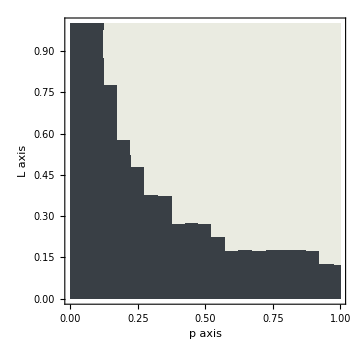

```mathematica
simulation5a=Import["simulation5a.wl"];
simulationRescaled=SortBy[simulation5a,#[[1;;2]]&]/. {x_,y_,z_}:>{x,y,Min[z,1]};
img=ListDensityPlot[
simulationRescaled,
Mesh->None,
InterpolationOrder->0,
PlotRange->{Full,Full,{0,1}},
PlotRangeClipping->False,
FrameLabel->{"p axis","L axis"},
ColorFunction->(ColorData["GrayTones"][1-0.8*Round[#]]&),
ColorFunctionScaling->False,
ImageSize->Medium
]
```

18:13:39

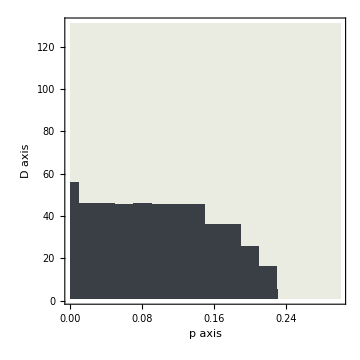

Fig5b.png

simulation5b.wl

```mathematica
(*Test for failure of propagation for varying p and D*)
(*Case 1: Additive heterogenerity*)
If[Not[TrueQ[filename=="Fig5b.png"]],simulation={};]
filename="Fig5b.png";
pos=5;width=4;L=0.5;
simulation={};
minP=0;maxP=0.3;dP=0.02;
minD=1;maxD=140;dD=10;
maxSteps=(Floor[(maxP-minP)/dP]+1)(Floor[(maxD-minD)/dD]+1);
Print[DateString[{"Hour",":","Minute",":","Second"}]]
(*timeList={};*)
Monitor[
i=0;
Do[
Do[
If[MemberQ[simulation,{p,D2,_}],i=i+1;Continue[]];
g[v_,x_]=-v *Boole[x>0] *Boole[x<L];
mesh=ToElementMesh[Line[{{xmin},{xmax}}],MaxCellMeasure->0.1];
{V1,W1}=NDSolveValue[{D[u[t,x],t]==Laplacian[u[t,x],{x}]+u[t,x] (1-u[t,x]) (u[t,x]-α)-w[t,x]+p g[u[t,x],x]+NeumannValue[0,x==xmin||x==xmax],τ D[w[t,x],t]==D2 Laplacian[w[t,x],{x}]+u[t,x]-γ w[t,x]+NeumannValue[0,x==xmin||x==xmax],
(*τ D[w[t,x],t]==u[t,x]-γ w[t,x],*)
u[0,x]==0.5 (1+Cos[Pi (x-pos)/width])*Boole[Abs[x-pos]<=width],
w[0,x]==0},
{u,w},
{t,0,maxtime},
Element[x,mesh],
Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}
];
lastP=p;
lastD=D2;
peaks=Length[FindPeaks[Table[V1[t,xmin], {t, 0, maxtime,0.1}],Automatic,Automatic,0.5]];
AppendTo[simulation,{p,D2,peaks}];
i=i+1;
,{p,minP,maxP,dP}]
,{D2,minD,maxD,dD}]
,Row[{ProgressIndicator[i,{1,maxSteps}]," ",PercentForm[N[i/maxSteps],3],", Last: (",lastP,", ",lastD,"), ",If[peaks>0,"Propagacion","Bloqueo"]}]
]
simulationRescaled=SortBy[simulation,#[[1;;2]]&]/. {x_,y_,z_}:>{x,y,Min[z,1]};
img=ListDensityPlot[
simulationRescaled,
Mesh->None,
InterpolationOrder->0,
PlotRange->{Full,Full,{0,1}},
PlotRangeClipping->False,
FrameLabel->{"p axis","D axis"},
ColorFunction->(ColorData["GrayTones"][1-0.8*Round[#]]&),
ColorFunctionScaling->False,
ImageSize->Medium
]
Export[filename,img]
Export["simulation5b.wl",simulation]
```

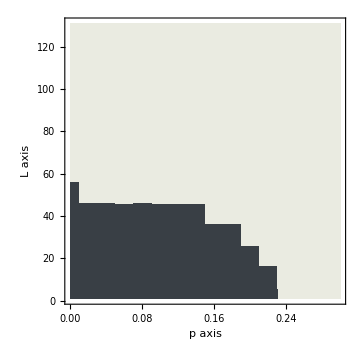

```mathematica
simulation5b=Import["simulation5b.wl"];
simulationRescaled=SortBy[simulation5b,#[[1;;2]]&]/. {x_,y_,z_}:>{x,y,Min[z,1]};
img=ListDensityPlot[
simulationRescaled,
Mesh->None,
InterpolationOrder->0,
PlotRange->{Full,Full,{0,1}},
PlotRangeClipping->False,
FrameLabel->{"p axis","L axis"},
ColorFunction->(ColorData["GrayTones"][1-0.8*Round[#]]&),
ColorFunctionScaling->False,
ImageSize->Medium
]
```